```mathematica
(*Se van a importar los datos*)
datosAu30=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\COMSOL\\Au_sph_30_prueba.csv"];
datosAu30extrafine=Import["C:\\Users\\Nanoplasmonics\\Documents\\Github\\Tesis-de-Licenciatura\\COMSOL\\Au_sph_radius30_extrafine.csv"];
datosgarcia=Import["C:\\Users\\Nanoplasmonics\\Documents\\Github\\Tesis-de-Licenciatura\\COMSOL\\garcia.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Au30=Drop[datosAu30,1];
datos1Au30extra=Drop[datosAu30extrafine,1];
datosgarcia1=Drop[datosgarcia,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
lambdadatosAu30=datos1Au30[[All,1]];
lambdadatosAu30extra=datos1Au30extra[[All,1]];
lambdadatosgarcia=h c/datosgarcia1[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
au30Cabs=Transpose[{lambdadatosAu30,datos1Au30[[All,3]]*(10^(18))}];
au30Cext=Transpose[{lambdadatosAu30,datos1Au30[[All,4]]*(10^(18))}];
au30Csca=Transpose[{lambdadatosAu30,datos1Au30[[All,2]]*(10^(18))}];
au30Cabsextra=Transpose[{lambdadatosAu30extra,datos1Au30extra[[All,3]]*(10^(18))}];
au30Cscaextra=Transpose[{lambdadatosAu30extra,datos1Au30extra[[All,2]]*(10^(18))}];
garciaCext=Transpose[{lambdadatosgarcia,datosgarcia1[[All,2]]}];
```

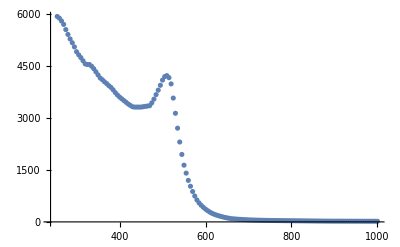

```mathematica
ListPlot[au30Cabs,PlotRange->All]
```

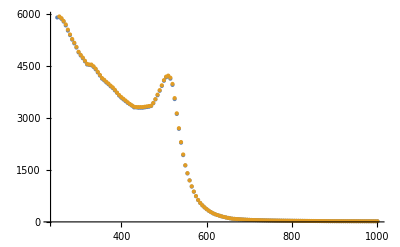

```mathematica
ListPlot[{au30Cabsextra,au30Cabs},PlotRange->All]
```

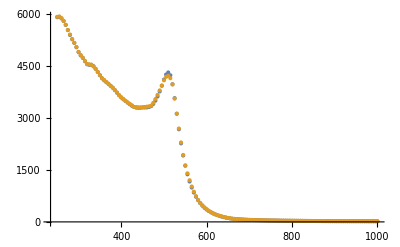

```mathematica
ListPlot[{auCabsMie15,au30Cabsextra},PlotRange->All]
```

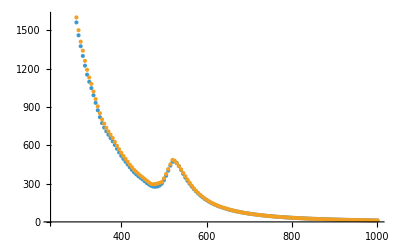

```mathematica
ListPlot[{auCscaMie15,au30Csca}]
```

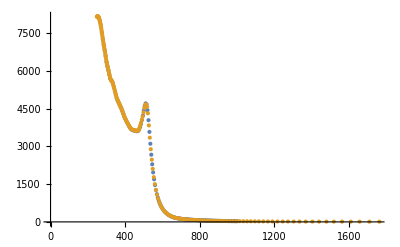

```mathematica
ListPlot[{auCextMie15,garciaCext}]
```

```mathematica
Length[au30LambdaCabs[[All,2]]]
Length[auCabsMie[[All,2]]]
```

151

161

```mathematica
ListPlot[Transpose[{lambdadatosAu30lambda,(Abs[au30LambdaCabs[[All,2]]-auCabsMie[[All,2]]]/au30LambdaCabs[[All,2]])*100}]]
```

Thread::tdlen: Objects of unequal length in {19100.,19000.,18900.,18700.,18600.,18400.,18300.,18300.,18300.,18300.,18400.,18500.,18600.,18700.,18900.,19100.,19300.,19500.,19800.,20000.,20100.,20300.,20500.,20700.,20800.,21000.,21200.,21300.,21500.,21600.,21800.,21900.,22100.,22200.,22400.,22500.,22600.,22800.,23000.,23200.,23400.,23600.,23800.,24000.,24100.,24500.,25000.,25600.,26200.,26800.,«301»}+{-18954.6,-18858.7,-18702.,-18535.5,-18370.1,-18206.6,-18116.8,«37»,-23995.7,-24313.,-24732.5,-25246.4,-25862.7,-26583.2,«101»} cannot be combined.

-Graphics-

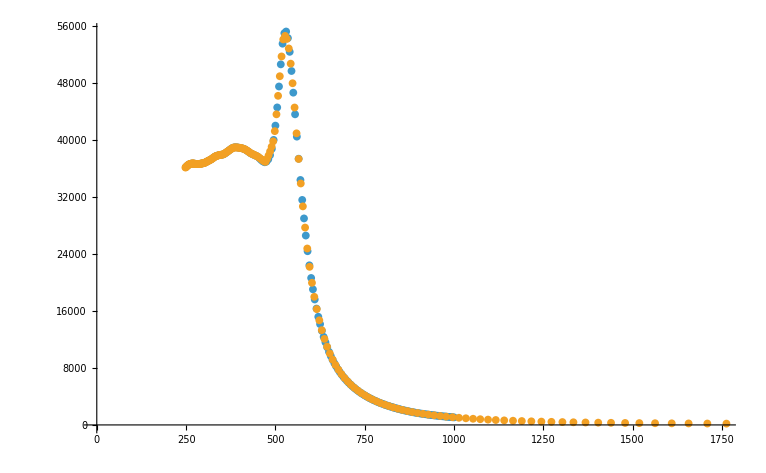

```mathematica
ListPlot[{auCextMie,comsol}]
```